# Elastics Scattering

```mathematica
mp={938.27203,1};
mO14={13048.92,14};
mC12={11178,12};
c=299.792458; (* mm/ns *)
T=260;
mInc=mO14;
mTar=mC12;
γBeam=(mInc[[1]]+mInc[[2]] T)/mInc[[1]];
βBeam=√(1-1/γBeam^2);
Lz[β_]:={{1/(√(1-β^2)),0,0,β/(√(1-β^2))},{0,1,0,0},{0,0,1,0},{β/(√(1-β^2)),0,0,1/(√(1-β^2))}};
Rz[θ_]:={{1,0,0,0},{0,Cos[θ],-Sin[θ],0},{0,Sin[θ],Cos[θ],0},{0,0,0,1}}
Ry[θ_]:={{1,0,0,0},{0,Cos[θ],0,Sin[θ]},{0,0,1,0},{0,-Sin[θ],0,Cos[θ]}}
(* title Lorentz operator *)
L[β_,θ_,ϕ_]:= Rz[ϕ].Ry[θ].Lz[β].Ry[-θ].Rz[-ϕ]
KE[V_,mass_]:=V[[1]]-mass[[1]]
KEoverA[V_,mass_]:=(V[[1]]-mass[[1]])/mass[[2]]
Momentum[A_]:=Norm[A[[2;;4]]]
βfromV[A_]:=Momentum[A]/A[[1]]
PolarAngle[A_]:=If[A[[2]]==0 && A[[3]]==0,{0,0},{ArcTan[A[[2]],A[[3]]],ArcTan[A[[4]],Norm[A[[2;;3]]]]}] (* ϕ, θ *)
FL[P_]:=Module[{ang},
ang=PolarAngle[P];
2 1400/(Abs[√3 Cos[ang[[1]]]Sin[ang[[2]]]]+Cos[ang[[2]]])]
ToF[P_]:=FL[P]/(βfromV[P] c)
SpVpp[P1_,P2_]:=(1+γBeam)mp[[1]]-γBeam mp[[1]](1/(√(1-βfromV[P1]^2))+1/(√(1-βfromV[P2]^2)))+γBeam βBeam mp[[1]] (βfromV[P1]/(√(1-βfromV[P1]^2))Cos[PolarAngle[P1][[2]]]+βfromV[P2]/(√(1-βfromV[P2]^2))Cos[PolarAngle[P2][[2]]])
SpV[P1_,P2_]:=mInc[[1]]+mTar[[1]]γBeam-γBeam(P1[[1]]+P2[[1]])+γBeam βBeam (P1[[4]]+P2[[4]])
ModeList[list_,bin_]:=bin[[1]]+(Ordering[BinCounts[list,bin],-1][[1]]-1)bin[[3]]
```

## General

```mathematica
Generator[θin_,ϕin_,θ_,ϕ_]:={
(* 1*)P1i={mInc[[1]]+mInc[[2]]T,√(2mInc[[1]]mInc[[2]] T+(mInc [[2]]T)^2)Cos[ϕin]Sin[θin],√(2mInc[[1]]mInc[[2]] T+(mInc [[2]]T)^2)Sin[ϕin]Sin[θin],√(2mInc[[1]]mInc[[2]] T+(mInc [[2]]T)^2)Cos[θin] },
P1it=Ry[-θin].Rz[-ϕin].P1i;
(* 2*)P2i={mTar[[1]],0,0,0},
Pci=1/2(P1it+P2i);
(* 3*)β=βfromV[Pci],
P1ict=Lz[-β].P1it;
P2ict=Lz[-β].P2i;
P1fct=Rz[ϕ].Ry[θ].P1ict;
P2fct=Rz[ϕ].Ry[θ].P2ict;
(* 4*)P1ic=Rz[ϕin].Ry[θin].P1ict,
(* 5*)P2ic=Rz[ϕin].Ry[θin].P2ict,
(* 6*)P1fc=Rz[ϕin].Ry[θin].P1fct,
(* 7*)P2fc=Rz[ϕin].Ry[θin].P2fct,
(* 8*)P1f=Rz[ϕin].Ry[θin].Lz[β].P1fct,
(* 9*)P2f=Rz[ϕin].Ry[θin].Lz[β].P2fct
}
Observable[list_]:=Table[{
(*1 ToF 1*)ToF[list[[i,1]]],
(*2 ToF 2*)ToF[list[[i,2]]],
(*3 Angle 1*)PolarAngle[list[[i,1]]],
(*4 Angle 2*)PolarAngle[list[[i,2]]],
(*5 Sp *)SpV[list[[i,1]],list[[i,2]]],
(*6 Δθ *)(PolarAngle[list[[i,1]]][[2]]+PolarAngle[list[[i,2]]][[2]])180/π,
(*7 Δϕ *)If[(PolarAngle[list[[i,1]]][[1]]-PolarAngle[list[[i,2]]][[1]])180/π>90,(PolarAngle[list[[i,1]]][[1]]-PolarAngle[list[[i,2]]][[1]])180/π-180,(PolarAngle[list[[i,1]]][[1]]-PolarAngle[list[[i,2]]][[1]])180/π+180],
(*8 KE 1 *) KE[list[[i,1]],mInc],
(*9 KE 2 *) KE[list[[i,2]],mTar],
(*10 KE1+KE2 *) KE[list[[i,1]],mInc]+KE[list[[i,2]],mTar]
},{i,1,Length[list]}];
ParaPlot[olist_,n_]:=GraphicsGrid[{
{Histogram[{Table[olist[[i,1]],{i,1,n}],Table[olist[[i,2]],{i,1,n}]},{7, 20,0.2},Frame->True,FrameLabel->{"ToF1, ToF2","Counts"},GridLines->Automatic],
Histogram[{Table[olist[[i,3,2]] 180/π,{i,1,n}],Table[olist[[i,4,2]] 180/π,{i,1,n}]},Frame->True,FrameLabel->{"θ1, θ2","Counts"},GridLines->Automatic]
},
{Histogram[{Table[olist[[i,6]],{i,1,n}]},Frame->True,FrameLabel->{"Δθ","Counts"},GridLines->Automatic],
Histogram[{Table[olist[[i,7]],{i,1,n}]},Frame->True,FrameLabel->{"Δϕ","Counts"},GridLines->Automatic]
},
{Histogram[{Table[olist[[i,8]]/mInc[[2]],{i,1,n}],Table[olist[[i,9]]/mTar[[2]],{i,1,n}]},Frame->True,FrameLabel->{"T1, T2 [MeV/A]","Counts"},GridLines->Automatic],
DensityHistogram[Table[{olist[[i,7]],olist[[i,6]]},{i,1,n}],Frame->True,FrameLabel->{"Δϕ","Δθ"},GridLines->Automatic]
},
{Histogram[{Table[olist[[i,10]],{i,1,n}]},Frame->True,FrameLabel->{"T1+T2","Counts"},GridLines->Automatic],
Histogram[{Table[olist[[i,5]],{i,1,n}]},Frame->True,FrameLabel->{"Sp","Counts"},GridLines->Automatic]
},
{DensityHistogram[Table[{olist[[i,3,2]] 180/π,olist[[i,1]]},{i,1,n}],{{1},{0.25}},PlotRange->{{20,70},{7,20}},Frame->True,FrameLabel->{"θ1","ToF1"},GridLines->Automatic],
DensityHistogram[Table[{olist[[i,4,2]] 180/π,olist[[i,2]]},{i,1,n}],{{1},{0.25}},PlotRange->{{20,70},{7,20}},Frame->True,FrameLabel->{"θ2","ToF2"},GridLines->Automatic]
}
},ImageSize->800]
```

```mathematica
Manipulate[
GraphicsGrid[{{
TableForm[Generator[θin °,ϕin °,θ °,ϕ °]],
Graphics3D[{
Arrow[{{0,0,0},{0,0,1000}}],
Arrow[{{0,0,0},{500,0,0}}],
Arrow[{{0,0,0},{0,500,0}}],
Green,Arrow[{-P1i[[2;;4]],{0,0,0}}],
Red,Arrow[{{0,0,0},P1f[[2;;4]]}],
Blue,Arrow[{{0,0,0},P2f[[2;;4]]}],
Pink,Arrow[{{0,0,0},P1fc[[2;;4]]}],
Cyan,Arrow[{{0,0,0},P2fc[[2;;4]]}]
}]
}},ImageSize->800]
,{{θin,0},-90,90},{{ϕin,0},-180,180},{{θ,90},0,180},{{ϕ,0},-180,180}]
```

### Generate distribution For Polarized Target

```mathematica
(* isotropic distribution and polarized *)
Manipulate[PolarPlot[{1,1+P 0.3 Sin[2θ]},{θ,0,2π}],{P,0,1}]
```

```mathematica
SphericalPlot3D[{1,(1+0.3Sin[2θ]Cos[ϕ])},{θ,0,π},{ϕ,-π,π},PlotStyle->{Directive[Opacity[0.5],Red],Directive[Opacity[0.5],Blue]}]
```

-Graphics3D-

```mathematica
Manipulate[Plot[{Sin[θ],(1+P 0.3 Sin[2θ])Sin[θ]},{θ,0,π},PlotRange->{0,2}],{P,0,1}]
```

```mathematica
(* to generate the distribution *)
dΩ=f[θ]Sin[θ]dθ dϕ = d(g[θ]) dϕ
(* thus *)
g[θ]=Integrate[f[θ] Sin[θ],θ]
(* Thus get the g^-1 *)
Solve[2μ-1 == g[θ],θ]
(* g^-1[μ] is the distribution *)
```

### Other way to Genrate a Distribution

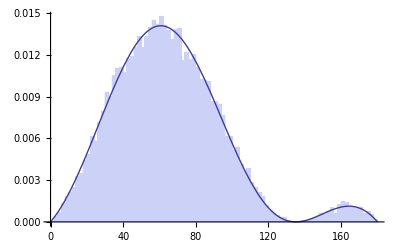

```mathematica
testProbDensity[x_]:=(1+Sin[2x °])Sin[x °]
testProbDist=ProbabilityDistribution[testProbDensity[x],{x,0,180,1}];
nfactor=Sum[Sin[x °],{x,0,180,1}]//N;
Cus=RandomVariate[ProbDist,20000];
Show[
Histogram[Cus,100,"ProbabilityDensity"],
Plot[PDF[testProbDist,x]/nfactor,{x,0,180},PlotStyle->Thick]
]
```

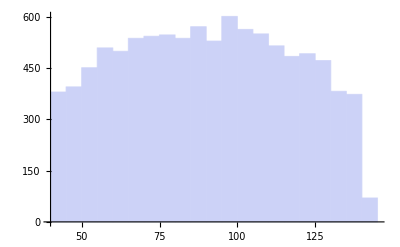

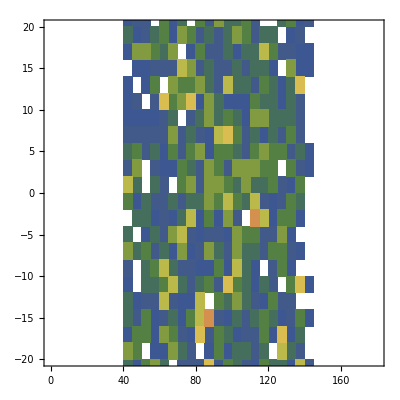

```mathematica
(* Generate data *)
n=10000;
Pol = 0;
ProbDensity[x_]:=(1+Pol 0.3Sin[2x °])Sin[x °];
ProbDist=ProbabilityDistribution[ProbDensity[x],{x,40,140,1}];
θList=RandomVariate[ProbDist,n] π/180;
ϕList=Table[ π RandomReal[{-1,1}],{i,1,n}];
θinList=Table[ RandomReal[{-0.03,0.03}],{i,1,n}];
ϕinList=Table[  RandomReal[{-0.04,0.06}],{i,1,n}];
DataList=Monitor[Table[Generator[θinList[[i]],ϕinList[[i]],θList[[i]],ϕList[[i]]][[8;;9]],{i,1,n}],i];
DensityHistogram[
Table[{θList[[i]] 180/π,ϕList[[i]] 180/π},{i,1,n}]
,{{5},{2}},ColorFunction->"DarkRainbow",PlotRange->{{0, 180},{-20,20}}
]
```

```mathematica
DataO=Observable[DataList];
```

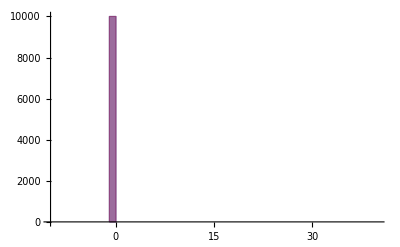

```mathematica
Histogram[
{Table[SpVpp[DataList[[i,1]],DataList[[i,2]]],{i,1,n}],
Table[SpV[DataList[[i,1]],DataList[[i,2]]],{i,1,n}]
},{-10,40,1},PlotRange->{{-10,40},All}
]
```

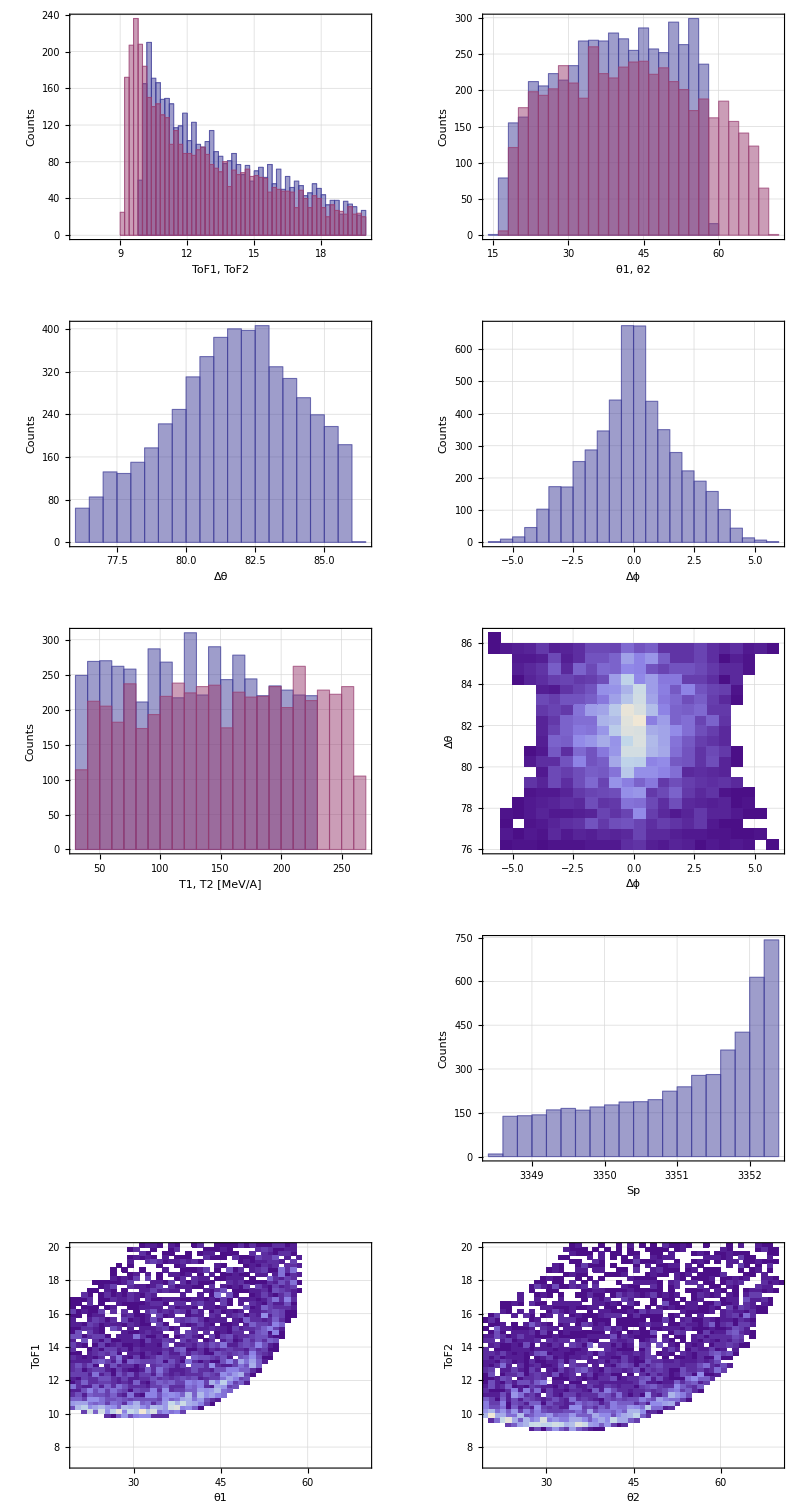

```mathematica
ParaPlot[DataO,n]
```

## Multi-Scattering

```mathematica
basis1[V_]:=Normalize[Cross[V[[2;;4]],{0,0,1}]]
basis2[V_]:=Normalize[Cross[basis1[V],V[[2;;4]]]]
Δr[V_,α_,β_]:=β(basis1[V]Cos[α]+basis2[V]Sin[α])
Scated[V_,β_]:=Normalize[V[[2;;4]]+Δr[V,RandomReal[{0,2π}],β]]
ScatV[mass_,V_,β_,ΔE_]:=Join[{mp+KE[V,mass]-ΔE}, √(2mp(KE[V,mass]-ΔE)+(KE[V,mass]-ΔE)^2)Scated[V,β]]
```

```mathematica
(* 256um Kapton, 2m Air, 100um Maylar *)
englostData=Interpolation[{
{25.0,6.00695},
{27.1,5.56307},
{30,5.07539},
{35,4.42979},
{40,3.94807},
{50,3.27243},
{60,2.81484},
{80,2.24327},
{100,1.892473},
{120,1.653914},
{140,1.480981},
{160,1.349884},
{180,1.246814},
{200,1.163668},
{220,1.09489},
{225.9,1.07786},
{240,1.037775},
{250,1.012578},
{260,0.989286}
}];
LateralData (* mm [sigma]*)=Interpolation[{
{20,5.424},
{25,3.812},
{27.1,3.428},
{30,3.023},
{35,2.523},
{40,2.173},
{50,1.712},
{60,1.420},
{80,1.062},
{100,0.853},
{120,0.715},
{140,0.617},
{160,0.544},
{180,0.487},
{200,0.442},
{220,0.404},
{225.9,0.395},
{240,0.373},
{250,0.360},
{260,0.347}
}];
```

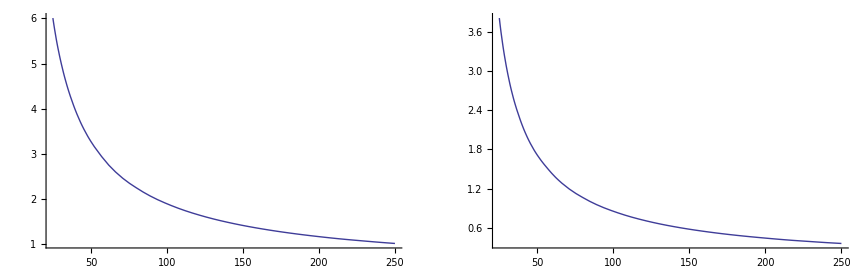

```mathematica
EngLost[T_]:=RandomVariate[NormalDistribution[englostData[T],0.184]](*MeV *)
ScatAng[T_]:=RandomVariate[NormalDistribution[0,LateralData [T]]](*mm *)
GraphicsGrid[{{Plot[englostData[t],{t,25, 250},PlotRange->{0,All},ImageSize->400],Plot[LateralData [t],{t,25, 250},PlotRange->{0,All}]}}]
```

```mathematica
MSData=Table[
{ScatV[mInc,DataList[[i,1]],ScatAng[KE[DataList[[i,1]],mInc]],EngLost[KE[DataList[[i,1]],mInc]]],
ScatV[mTar,DataList[[i,2]],ScatAng[KE[DataList[[i,2]],mTar]],EngLost[KE[DataList[[i,2]],mTar]]]
},{i,1,n}];
```

```mathematica
(* in case skipping the Multi-scattering *)
MSData =DataList;
MSObserv=Observable[MSData];
```

```mathematica
Histogram[
Table[ArcCos[Normalize[MSData[[i,1]][[2;;4]]].Normalize[DataList[[i,1]][[2;;4]]]] 180/π,{i,1,n}]
]
```

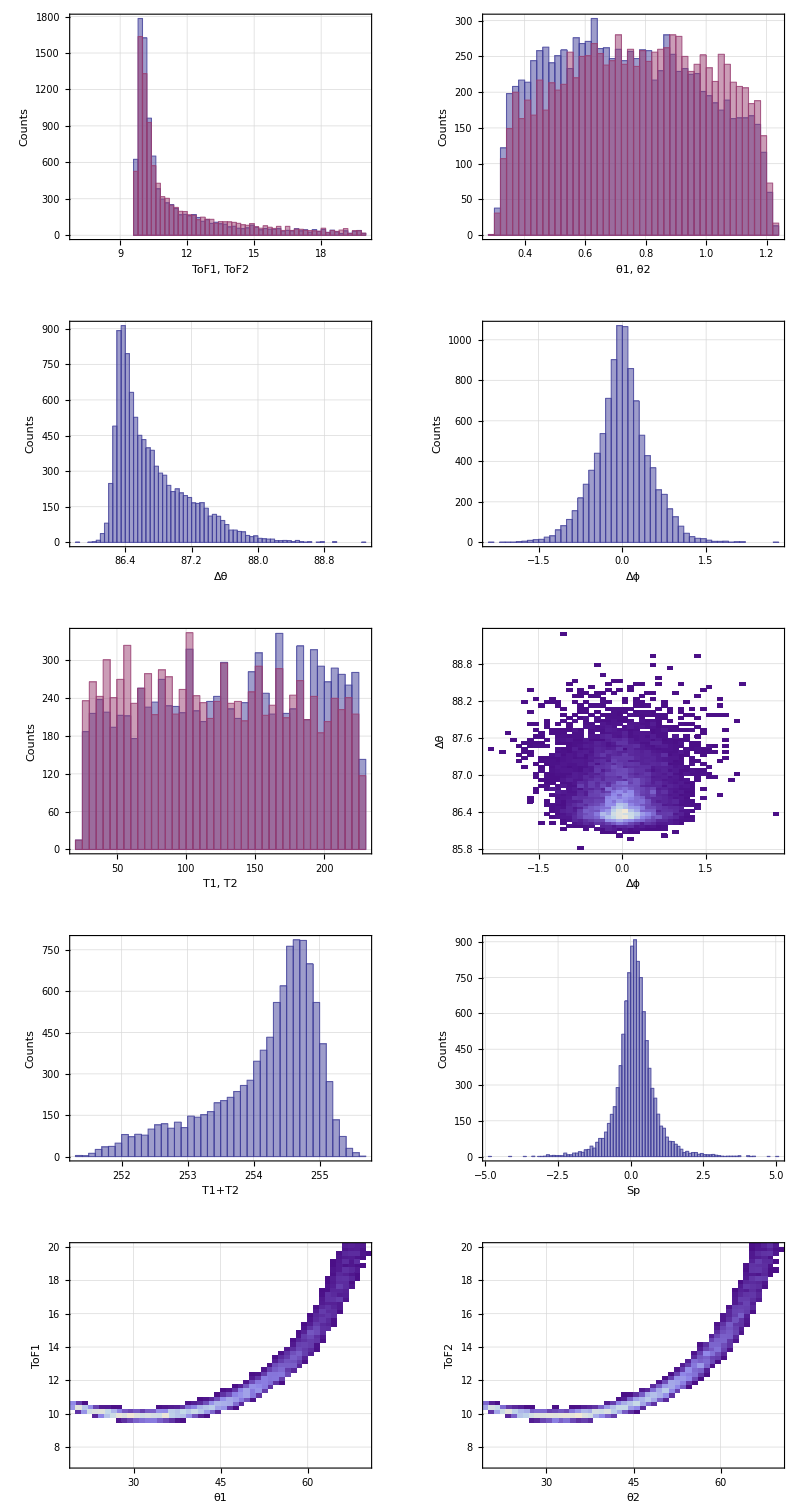

```mathematica
MSObserv=Observable[MSData];
ParaPlot[MSObserv,n]
```

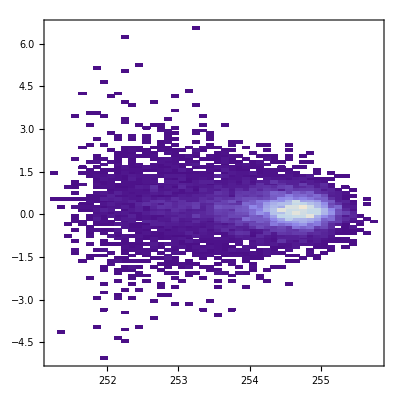

```mathematica
DensityHistogram[
Table[{MSObserv[[i,10]],MSObserv[[i,5]]},{i,1,n}]
]
```

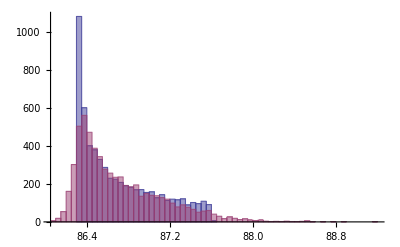

```mathematica
Histogram[{
Table[DataO[[i,6]],{i,1,n}],
Table[MSObserv[[i,6]],{i,1,n}]
}]
```

## Detector Resolution

```mathematica
(* the change of ToF but not angle *)
σTof=0.25;
MSToF1=Table[MSObserv[[i,1]]+RandomVariate[NormalDistribution[0,σTof]],{i,1,n}];
MSToF2=Table[MSObserv[[i,2]]+RandomVariate[NormalDistribution[0,σTof]],{i,1,n}];
```

```mathematica
MSXY1=Table[1022.37/({(√3)/2,0,1/2}.Normalize[MSData[[i,1]][[2;;4]]])Normalize[MSData[[i,1]][[2;;4]]],{i,1,n}];
MSXY2=Table[1022.37/({-(√3)/2,0,1/2}.Normalize[MSData[[i,2]][[2;;4]]])Normalize[MSData[[i,2]][[2;;4]]],{i,1,n}];
```

```mathematica
Rot1=RotationMatrix[60°,{0,-1,0}];
Rot2=RotationMatrix[60°,{0,1,0}];
```

```mathematica
MWDCcoord1=Table[Rot1.MSXY1[[i]],{i,1,n}];
MWDCcoord2=Table[Rot2.MSXY2[[i]],{i,1,n}];
```

```mathematica
Graphics3D[{
Arrow[{{0,0,0},{0,0,1400}}],
Arrow[{{0,0,0},Rot1.{0,0,1400}}],
Arrow[{{0,0,0},Rot2.{0,0,1400}}],
PointSize[Small],
{Hue[0.3],Point[MWDCcoord1]},
Point[MWDCcoord2],
Blue,Point[MSXY1],
Blue,Point[MSXY2]
}]
```

-Graphics3D-

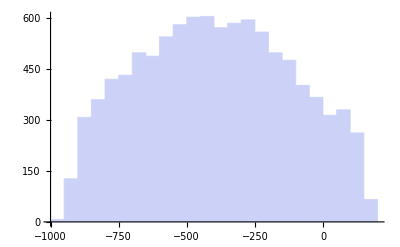

```mathematica
Histogram[Table[MWDCcoord1[[i,1]],{i,1,n}]]
```

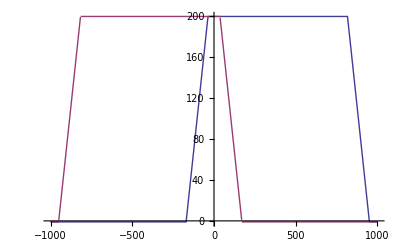

```mathematica
f[x_]:=Piecewise[{{3/2(x+170),200 2/3-170>x>-170},{200,200 (-2/3)+950>x>200 2/3-170},{-3/2(x-950),950>x>200 (-2/3)+950}},-1]
Plot[{f[x],f[-x]},{x,-1000,1000}]
```

```mathematica
(* Filter events by MWDC detection area , Filter will select MWDC pos and ToF*)
fMWDCcoord=Select[
Table[
If[f[-MWDCcoord1[[i,1]]]>Abs[MWDCcoord1[[i,2]]] && f[MWDCcoord2[[i,1]]]>Abs[MWDCcoord2[[i,2]]],{MWDCcoord1[[i]],MWDCcoord2[[i]],MSToF1[[i]],MSToF2[[i]]},{{0,0,0},{0,0,0}}],{i,1,n}]
,#≠{{0,0,0},{0,0,0}}&];
m=Length[fMWDCcoord]
```

349

```mathematica
ModeList[Table[fMWDCcoord[[i,1,1]],{i,1,m}],{-1000,200,10}]
```

-230

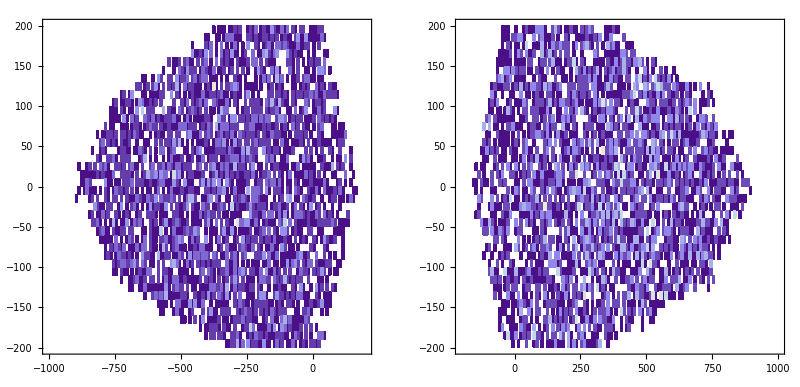

```mathematica
GraphicsGrid[{{DensityHistogram[
Table[{fMWDCcoord[[i,1,1]],fMWDCcoord[[i,1,2]]},{i,1,m}],{{10},{10}},PlotRange->{{-1000,200},{-200,200}}
],
DensityHistogram[
Table[{fMWDCcoord[[i,2,1]],fMWDCcoord[[i,2,2]]},{i,1,m}],{{10},{10}},PlotRange->{{-200,1000},{-200,200}}
]}},ImageSize->800]
```

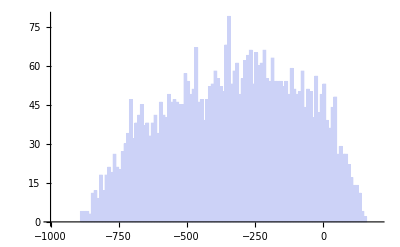

```mathematica
Histogram[Table[fMWDCcoord[[i,1,1]],{i,1,m}],{-1000,200,10}]
```

```mathematica
Pos1=Table[Rot2.{
fMWDCcoord[[i,1,1]]+RandomVariate[NormalDistribution[0,0.3]],
fMWDCcoord[[i,1,2]]+RandomVariate[NormalDistribution[0,5]],
fMWDCcoord[[i,1,3]]
},{i,1,m}];
Pos2=Table[Rot1.{
fMWDCcoord[[i,2,1]]+RandomVariate[NormalDistribution[0,0.3]],
fMWDCcoord[[i,2,2]]+RandomVariate[NormalDistribution[0,5]],
fMWDCcoord[[i,2,3]]
},{i,1,m}];
reactionPos=Table[{
0RandomVariate[NormalDistribution[0,10]],
0RandomVariate[NormalDistribution[0,10]],
0
},{i,1,m}];
```

```mathematica
Graphics3D[{
Arrow[{{0,0,0},{0,0,1400}}],
Arrow[{{0,0,0},Rot1.{0,0,1400}}],
Arrow[{{0,0,0},Rot2.{0,0,1400}}],
Point[Pos1],
Point[Pos2],
Blue,PointSize[Small],Point[MSXY1], Point[MSXY2]
}]
```

-Graphics3D-

```mathematica
FL1=Table[Norm[Pos1[[i]]-reactionPos[[i]]] 1400/1022.37,{i,1,m}];
FL2=Table[Norm[Pos2[[i]]-reactionPos[[i]]] 1400/1022.37,{i,1,m}];
β1=Table[FL1[[i]]/(fMWDCcoord[[i,3]] c),{i,1,m}];
β2=Table[FL2[[i]]/(fMWDCcoord[[i,4]]  c),{i,1,m}];
T1=Table[mInc[[1]]/(√(1-β1[[i]]^2))-mInc[[1]],{i,1,m}];
T2=Table[mTar[[1]]/(√(1-β2[[i]]^2))-mTar[[1]],{i,1,m}];
TotalT=Table[T1[[i]]+T2[[i]],{i,1,m}];
```

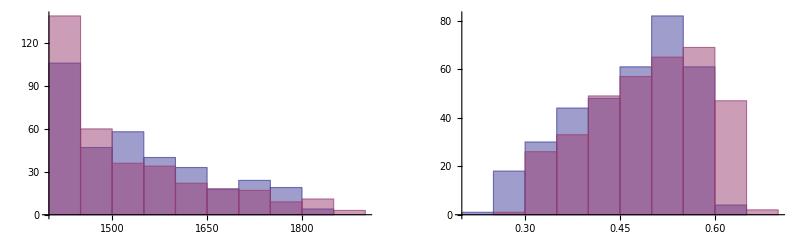

```mathematica
GraphicsGrid[{{Histogram[{FL1,FL2}],Histogram[{β1,β2}]}},ImageSize->800]
```

```mathematica
Histogram[TotalT,{200,350,2},ImageSize->600,GridLines->{{50,100,150,200,250,300,350,400},Automatic},Frame->True,FrameLabel->{"T1+T2","Counts"}]
```

$Aborted

```mathematica
ModeList[TotalT,{0,400,4}]
```

252

```mathematica
Measure=Table[
{Join[{T1[[i]]+mInc[[1]]},√(2 mInc[[1]] T1[[i]]+T1[[i]]^2)Normalize[Pos1[[i]]]],
Join[{T2[[i]]+mTar[[1]]},√(2 mTar[[1]] T2[[i]]+T2[[i]]^2)Normalize[Pos2[[i]]]]
},{i,1,m}];
MeasureObser=Observable[Measure];
```

```mathematica
ModeList[Table[MeasureObser[[i,1]],{i,1,m}] ,{7,20,0.1}]
ModeList[Table[MeasureObser[[i,6]],{i,1,m}] ,{86,90,0.1}]
```

10.2

86.4

```mathematica
momt1=Table[{Measure[[i,1,4]],Norm[Measure[[i,1,2;;3]]]},{i,1,m}];
```

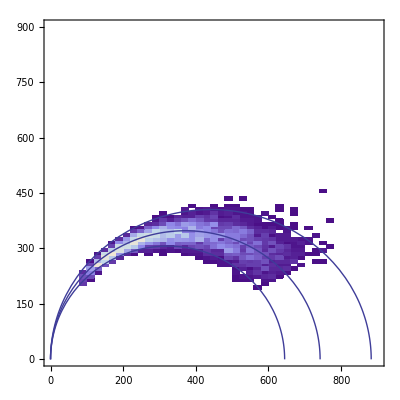

```mathematica
Show[
DensityHistogram[momt1,PlotRange->{{0,900},{0,900}}],
ParametricPlot[{√(T (2 mp+T)) Cos[(θNN °)/2]^2,(√(mp T) Sin[θNN °])/(√2)},{θNN,0,180}],
ParametricPlot[{√(200 (2 mp+200)) Cos[(θNN °)/2]^2,(√(mp 200) Sin[θNN °])/(√2)},{θNN,0,180}],
ParametricPlot[{√(350 (2 mp+350)) Cos[(θNN °)/2]^2,(√(mp 350) Sin[θNN °])/(√2)},{θNN,0,180}]
]
```

```mathematica
Table[{√(350 (2 mp+350)) Cos[(θNN °)/2]^2,(√(mp 350) Sin[θNN °])/(√2)},{θNN,36,180-36,18}]//TableForm
```

798.477 | 238.178
700.828 | 327.824
577.783 | 385.38
441.387 | 405.213
304.991 | 385.38
181.946 | 327.824
84.2974 | 238.178

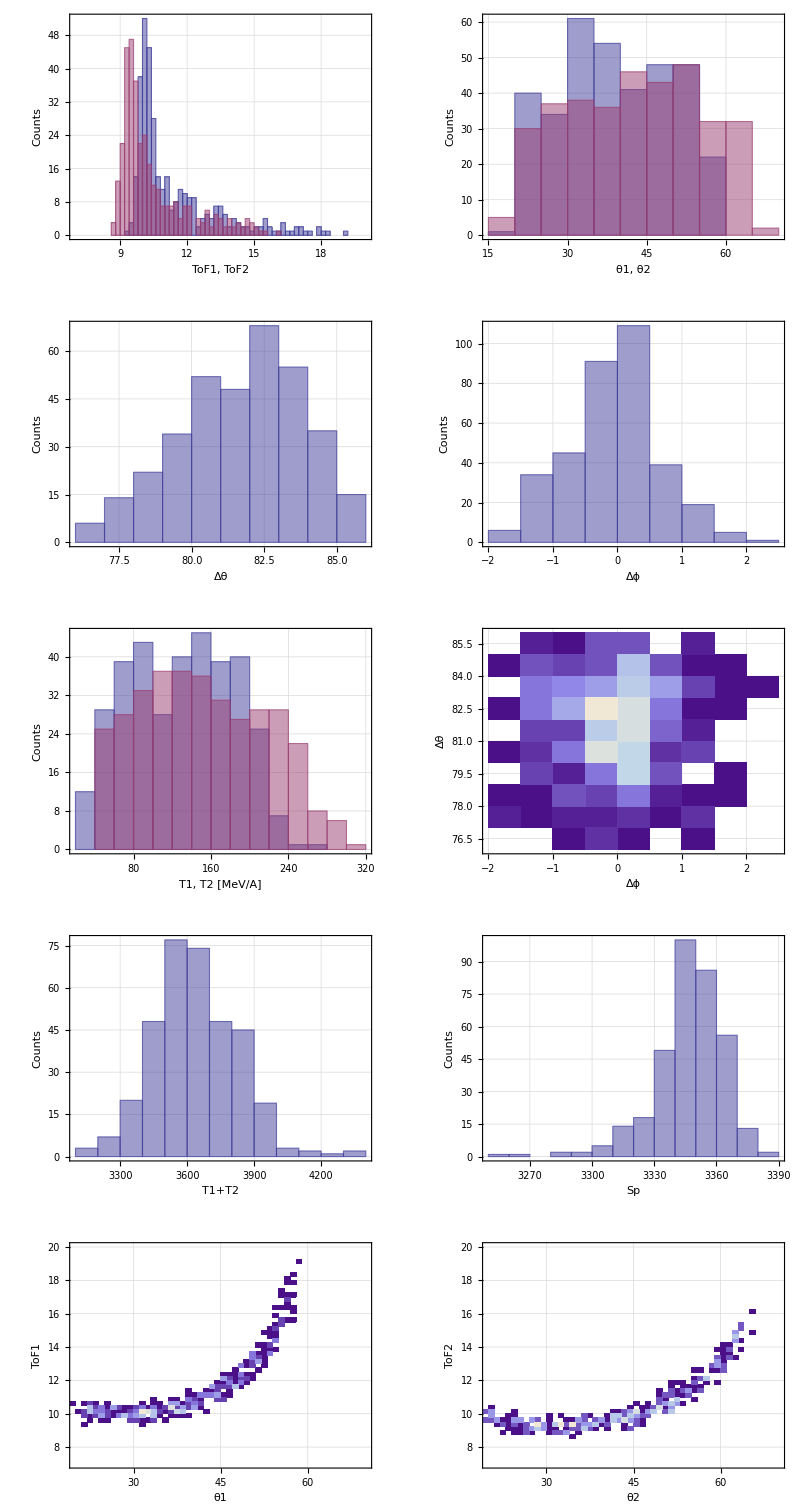

```mathematica
ParaPlot[MeasureObser,m]
```

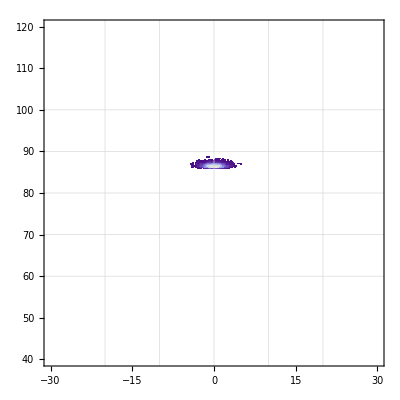

```mathematica
DensityHistogram[
Table[{MeasureObser[[i,7]],MeasureObser[[i,6]]},{i,1,m}]
,{{0.2},{0.2}},PlotRange->{{-30,30},{40,120}}, GridLines->{{-20,-10,0,10,20},{60,70,80,90,100}}
]
```

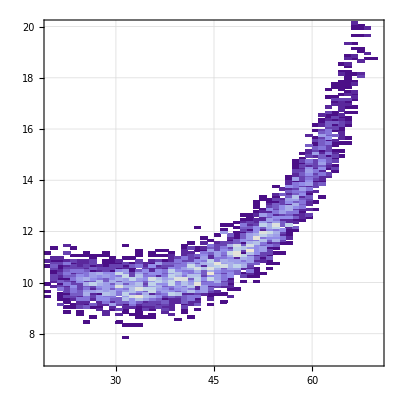

```mathematica
DensityHistogram[
Table[{MeasureObser[[i,3,2]] 180/π,MeasureObser[[i,1]]},{i,1,m}],{{1},{0.1}}, GridLines->Automatic,PlotRange->{{20,70},{7,20}}
]
```

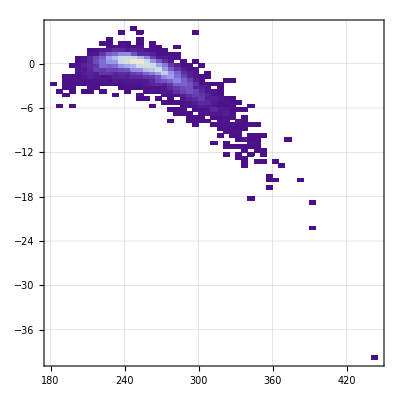

```mathematica
DensityHistogram[
Table[{MeasureObser[[i,10]],MeasureObser[[i,5]]},{i,1,m}], GridLines->Automatic
]
```

```mathematica
Mean[MSToF1]
StandardDeviation[MSToF1]
```

11.8723

2.61312

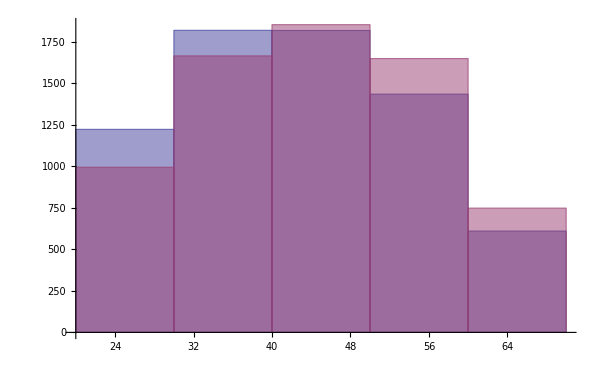

```mathematica
Histogram[{Table[MeasureObser[[i,3,2]] 180/π,{i,1,m}],Table[MeasureObser[[i,4,2]] 180/π,{i,1,m}]},{20,70,10},ImageSize->600]
```

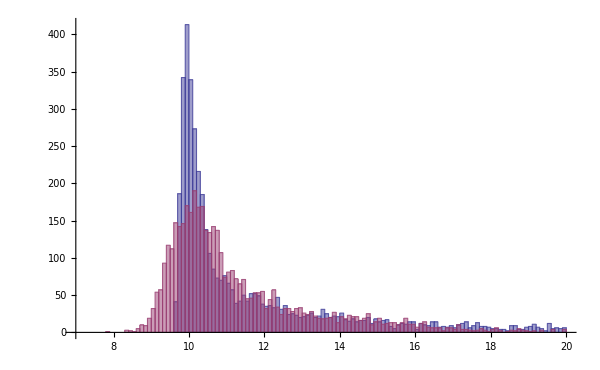

```mathematica
Histogram[{Table[MSObserv[[i,1]],{i,1,m}],Table[MeasureObser[[i,1]],{i,1,m}]},{7,20,0.1},ImageSize->600]
```

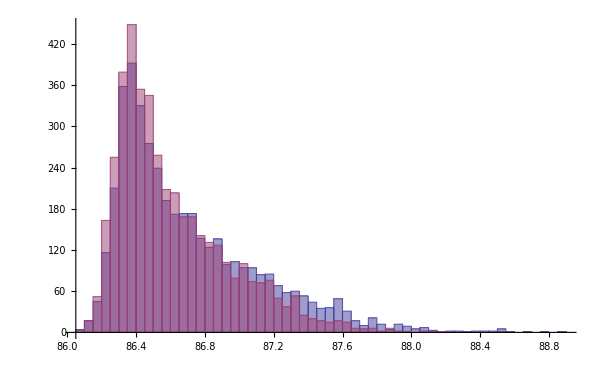

```mathematica
Histogram[{Table[MSObserv[[i,6]],{i,1,m}],Table[MeasureObser[[i,6]],{i,1,m}]},ImageSize->600]
```

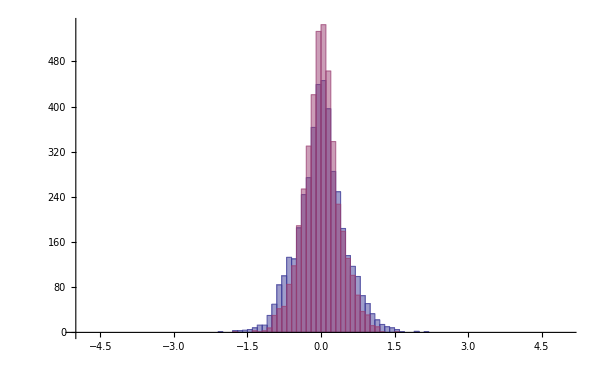

```mathematica
Histogram[{Table[MSObserv[[i,7]],{i,1,m}],Table[MeasureObser[[i,7]],{i,1,m}]},{-5,5,0.1},ImageSize->600]
```

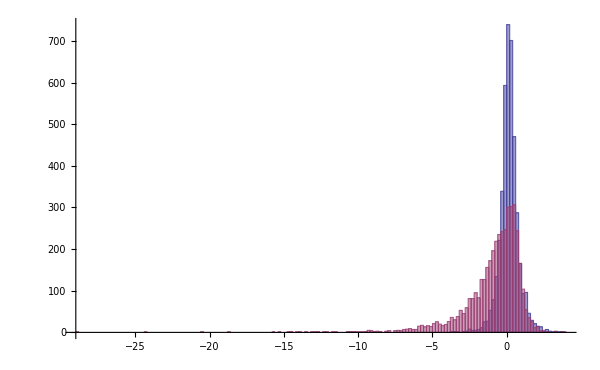

```mathematica
Histogram[{Table[MSObserv[[i,5]],{i,1,m}],Table[MeasureObser[[i,5]],{i,1,m}]},ImageSize->600]
```